### Associations

```mathematica
vecA=Association[{"x"->{1,0,0},"y"->{0,1,0},"z"->{0,0,1},"-x"->{-1,0,0},"-y"->{0,-1,0},"-z"->{0,0,-1}}];
phaseA=Association[{"x"->0,"y"->π/2,"-x"->π,"-y"->-π/2,{Cos[θ],Sin[θ],0}->θ}];
```

### Pulses

#### Individual pulses

```mathematica
wait[τ_]={"w",τ};
p2x={"p",Ω,π/2,"x"};
p2y={"p",Ω,π/2,"x"};
px={"p",Ω,π ,"x"};
py={"p",Ω,π ,"y"};
pmx={"p",Ω,π,"-x"};
pmy={"p",Ω,π ,"-y"};
p2ϕ={"p",Ω,π/2,{Cos[θ],Sin[θ],0}};
```

#### Combined pulses

```mathematica
ramsey={p2x,wait[τ],p2ϕ};
spinEcho={p2x,wait[τ],px,wait[τ],p2ϕ};
xy8={p2x,wait[τ],px,wait[2τ],py,wait[2τ],px,wait[2τ],py,wait[2τ],py,wait[2τ],px,wait[2τ],py,wait[2τ],px,wait[τ],p2ϕ};
xy16={p2x,wait[τ],px,wait[2τ],py,wait[2τ],px,wait[2τ],py,wait[2τ],py,wait[2τ],px,wait[2τ],py,wait[2τ],px,wait[2τ],pmx,wait[2τ],pmy,wait[2τ],pmx,wait[2τ],pmy,wait[2τ],pmy,wait[2τ],pmx,wait[2τ],pmy,wait[2τ],pmx,wait[τ],p2ϕ};
xy8n[n_]:=Join[{p2x,wait[τ]},Flatten[ConstantArray[{px,wait[2τ],py,wait[2τ],px,wait[2τ],py,wait[2τ],py,wait[2τ],px,wait[2τ],py,wait[2τ],px,wait[2τ]},n],1][[;;-2]],{wait[τ],p2ϕ}];
```

#### Timing

```mathematica
blockDuration[pulse_]:=Table[With[{block=pulse[[i]]},Which[MemberQ[{"p",1},block[[1]]],block[[3]]/block[[2]],MemberQ[{"w",0},block[[1]]],block[[2]]]],{i,1,Length[pulse]}]
blockEnds[pulse_]:=Accumulate[blockDuration[pulse]]
blockStarts[pulse_]:=blockEnds[pulse]-blockDuration[pulse]
blockTimes[pulse_]:=Transpose@{blockStarts[pulse],blockEnds[pulse]}
```

### Hamiltonian

#### States

```mathematica
g={{1},{0}};e={{0},{1}};
```

#### Windows

```mathematica
tukey[a_,τ_,t0_,α_]=a TukeyWindow[(t-t0)/τ-0.5,α];
dirichlet[a_,τ_,t0_]=a DirichletWindow[(t-t0)/τ-0.5];
```

```mathematica
tukeyError[α_]=π/Integrate[TukeyWindow[t/π,α],{t,-∞,∞}];
```

#### TD Hamiltonian terms

```mathematica
amp[pulse_]:=Module[{α=0.01,pPos,pStart,pAmp,pDur,pαs},pPos=Flatten[Quiet[Position[pulse,x_/;x[[1]]=="p"]]];
pStart=blockStarts[pulse][[pPos]];
pAmp=tukeyError[α]pulse[[pPos,2]];
pDur=blockDuration[pulse][[pPos]];
pαs=ConstantArray[α,Length[pPos]];
Total[MapThread[tukey,{pAmp,pDur,pStart,pαs}]]]
```

```mathematica
phase[pulse_]:=Module[{pPos,pStart,pPhase,pDur,pαs},pPos=Flatten[Quiet[Position[pulse,x_/;x[[1]]=="p"]]];
pStart=blockStarts[pulse][[pPos]];
pPhase=pulse[[pPos,4]]/.phaseA;
pDur=blockDuration[pulse][[pPos]];
Total[MapThread[dirichlet,{pPhase,pDur,pStart}]]]
```

```mathematica
phase[ramsey]
```

θ DirichletWindow[-0.5+(2 (t-τ-π/(2 Ω)) Ω)/π]

#### Hamiltonian

```mathematica
amp[ramsey]
```

1.00503 Ω TukeyWindow[-0.5+(2 t Ω)/π,0.01]+1.00503 Ω TukeyWindow[-0.5+(2 (t-τ-π/(2 Ω)) Ω)/π,0.01]

```mathematica
H[pulse_]:=({{0, amp[pulse]Cos[2π f0 t+phase[pulse]]}, {amp[pulse]Cos[2π f0 t+phase[pulse]], 2π f0}})
```

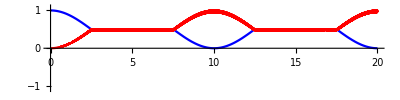

```mathematica
rep={Ω->2π 0.1,τ->5,θ->π,f0->30};
pulse0=spinEcho;
Ham=.;Ham[t_]=H[pulse0]/.rep;
ψ[t_]={c1[t],c2[t]};
init=ψ[0]=={1,0};
SE=ⅈ ψ'[t]==Ham[t].ψ[t];
sols=NDSolve[{SE,init},{c1,c2},{t,0,blockTimes[pulse0][[-1,-1]]/.rep},PrecisionGoal->12,MaxSteps->10^7,Method->"StiffnessSwitching"];
Plot[Evaluate[Flatten[{(Abs[#[t]]^2/.sols)&/@{c1,c2}}]],{t,0,blockTimes[pulse0][[-1,-1]]/.rep},PlotRange->{-1.1,1.1},ImageSize->Full,AspectRatio->1/4,PlotLegends->{"|0>","|1>","Clock","Pulse field","Pulse amplitude"},PlotStyle->{Blue,Red},PerformanceGoal->"Quality",PlotPoints->300]
```

```mathematica
rep
```

{Ω→0.628319,τ→5,θ→π,f0→100}

```mathematica
Cos[2π f0 t]/.rep,Cos[2π f0 t+phase[pulse0]] amp[pulse0]/(tukeyError[0.01]Ω)/.rep,amp[pulse0]/(tukeyError[0.01]Ω)/.rep
```

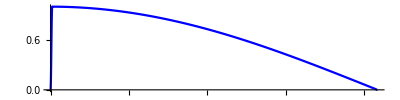

```mathematica
rep={Ω->2π 0.1,τ->5,θ->π,f0->.1};
Plot[Cos[2π f0 t+phase[pulse0]] amp[pulse0]/(tukeyError[0.01]Ω)/.rep,{t,0,blockDuration[xy8][[1]]/.rep},ImageSize->Full,AspectRatio->1/4,PlotLegends->{"Electric field during π/2 pulse"},PlotStyle->Blue,PerformanceGoal->"Quality",PlotPoints->300]
```

```mathematica
blockDuration[xy8][[1]]
```

π/(2 Ω)